## Derivatives

## Straight lines

### Formatting

```mathematica
DarkGreen:=Green//Darker//Darker
```

```mathematica
labelst[str_]:=Style[str,12,FontFamily->"Arial",Background->White]
```

```mathematica
Style[str,12,FontFamily->"Arial",Background->White]
```

str

```mathematica
myn[n_]:=labelst[If[Abs[n]<.0001,NumberForm[0.0,4],NumberForm[n,4]]]
```

```mathematica
myn[8.0^-5]
```

0.

```mathematica
Head[myn[8.9]]
```

Style

```mathematica
labelst[cu["a"]//TraditionalForm]
```

a^3-a

```mathematica
Remove[fsty]
```

```mathematica
fsty[f_,x_]:=Text[labelst[f[x]]//TraditionalForm]
```

```mathematica
fsty[cu,"a"]
```

a^3-a

### Point-slope form

```mathematica
ptsl[m_,p_,x_]:=m x+ p[[2]]-m p[[1]]
```

```mathematica
ptsl[m_,p_,x_]:=m (x-p[[1]])+ p[[2]]//Simplify
```

```mathematica
ptsl[3,{1,2},x]
```

-1+3 x

### Two-point form

```mathematica
tpl[p_,q_,x_]:=(p[[2]]-q[[2]])/(p[[1]]-q[[1]])(x-p[[1]])+p[[2]]//Simplify
```

```mathematica
tpl[{1,2},{0,-1},x]
```

-1+3 x

```mathematica
tpl[{0,-1},{1,2},x]
```

-1+3 x

```mathematica
tpl[{1,4},{5,2},x]
```

(9-x)/2

## Other definitions

```mathematica
cu[x_]:=x^3-x;cud[x_]:=cu'[x]
```

```mathematica
labelst[str_]:=Style[str,14,FontFamily->"Arial",Background->White];
tline[a_,x_]:=ptsl[cud[a],{a,cu[a]},x];
(*offs:=.3;*)
u[x_,offs_]:={x+offs,ptsl[cud[x],{x,cu[x]},x+offs]};
v[x_,offs_]:={x-offs,ptsl[cud[x],{x,cu[x]},x-offs]};
corner[x_,offs_]:={v[x,offs][[1]],u[x,offs][[2]]};
secline[a_,b_,x_]:=If[
a==b,
ptsl[cud[a],{a,cu[a]},x],
tpl[{a,cu[a]},{b,cu[b]},x]
]
```

```mathematica
u[.8,.3]
```

{1.1,-0.012}

```mathematica
v[.8,.3]
```

{0.5,-0.564}

```mathematica
corner[.8,.3]
```

{0.5,-0.012}

```mathematica
corner[x,.3]
```

{-0.3+x,-0.3-1. x+0.9 x^2+x^3}

```mathematica
seclineslope[a_,b_]:=If[
a==b,
cud[a],
(cu[b]-cu[a])/(b-a)]
```

```mathematica
secline[.9,1.2,x]
```

-2.268+2.33 x

```mathematica
seclineslope[.9,1.4]
```

3.03

```mathematica
(((x+h)^3-(x+h))-((x-h)^3-(x-h)))/((x+h)-(x-h))
```

(-2 h-(-h+x)^3+(h+x)^3)/(2 h)

```mathematica
Simplify[(-2 h-(-h+x)^3+(h+x)^3)/(2 h)]
```

-1+h^2+3 x^2

```mathematica
height[x_,offs_]:=(corner[x,offs]-v[x,offs])[[2]]
```

```mathematica
height[-.85,.05]
```

0.11675

## Tangent lines

```mathematica
tanline[f_,a_,x_]:=ptsl[f'[a],{a,f[a]},x]
```

```mathematica
sform[e_]:=e//TraditionalForm//labelst
```

```mathematica
x^2//sform
```

x^2

```mathematica
(#^3-#)&[x]//sform
```

x^3-x

```mathematica
(#^3-#)&'[x]//sform
```

3 x^2-1

```mathematica
Cos[#/Pi]&[x]
```

Cos[x/π]

## Demo of tangent lines

<script type=”text/javascript” src=”http://www.wolfram.com/cdf-player/plugin/v2.1/cdfplugin.js”></script>
<script type=”text/javascript”>
var cdf = new cdfplugin();
cdf.setDefaultContent(‘<a href=”http://www.wolfram.com/cdf-player/”><img  src=”Naive Tangent.png”></a>’);
cdf.embed(‘http://www.abstractmath.org/Mathematica/Naive Tangent.cdf’, 285, 357);
</script>

```mathematica
Module[{a,f},
Manipulate[Plot[
{f[x],tanline[f,a,x]},
{x,-1.7,1.7},
PlotRange->{{-1.7,1.7},{-2,2}},
PlotStyle->{Blue,Red},AspectRatio->40/34,ImageSize->200
],
{{a,-.85,Style["a",12]},-1.25,1.25},
{{f,(#^2)&,Style["function",12]},{(#^2)&->(x^2//sform),(#^3-#)&->(x^3-3x//sform),(Cos[Pi #])&->(Cos[Pi x]//sform),(Exp[#]-2)&->(e^x-2//sform)},
Background->White},
SaveDefinitions->True,Paneled->False
]
]
```

## Circle

```mathematica
Module[{a},
Manipulate[
Plot[
{Sqrt[1-x^2],-Sqrt[1-x^2]},
{x,-1.7,1.7},
PlotRange->{{-1.5,1.5},{-1.5,1.5}},
PlotStyle->{Blue,Blue},AspectRatio->1,ImageSize->200
],
{{a,Pi/4,Style["a",12]},.01,.99Pi},
SaveDefinitions->True,Paneled->False
]
]
```

```mathematica
Module[{a},
Manipulate[
ParametricPlot[
{Cos[a],Sin[a]},
{a,.01,.99Pi},
PlotStyle->{Red},AspectRatio->1,PlotRange->{{-1.5,1.5},{-1.5,1.5}},ImageSize->200
],
{{a,Pi/4,Style["a",12]},.01,.99Pi},
SaveDefinitions->True,Paneled->False
]
]
```

```mathematica
Module[{a},
Manipulate[
Graphics[
{Plot[
{Sqrt[1-x^2],-Sqrt[1-x^2]},
{x,-1.7,1.7},
PlotRange->{{-1.5,1.5},{-1.5,1.5}},
PlotStyle->{Blue,Blue},AspectRatio->1,ImageSize->200
],
ParametricPlot[
{Cos[a],Sin[a]},
{a,.01,.99Pi},
PlotStyle->{Red},AspectRatio->1,PlotRange->{{-1.5,1.5},{-1.5,1.5}},ImageSize->200
],
}
],
{{a,Pi/4,Style["a",12]},.01,.99Pi},
SaveDefinitions->True,Paneled->False
]
]
```

## Derivative' s value is slope of tangent line

### More definitions

```mathematica
myexp[e_]:=ToString[e//labelst,TraditionalForm]
```

```mathematica
myexp["x\\mapsto x^3-x"]
```

x\mapsto x^3-x

```mathematica
myexp["x^3-x"]
```

x^3-x

```mathematica
x^3-x//TraditionalForm//labelst
```

x^3-x

```mathematica
dvdef[f_,x_,h_]:=((f[x+h]-f[x])/h)
```

```mathematica
dvdef[cu,x,h]
```

(-h-x^3+(h+x)^3)/h

```mathematica
myn[dvdef[cu,.4,.2]]
```

-0.24

```mathematica
cu'[x]//TraditionalForm
```

3 x^2-1

### Calculations for input function, output slope

```mathematica
{.2,ptsl[cud[.2],{1,cu[.2]},.3]}
```

{0.2,0.424}

<script type=”text/javascript” src=”http://www.wolfram.com/cdf-player/plugin/v2.1/cdfplugin.js”></script>
<script type=”text/javascript”>
var cdf = new cdfplugin();
cdf.setDefaultContent(‘<a href=”http://www.wolfram.com/cdf-player/”><img  src=”Deriv is Slope of Tan Line.png”></a>’);
cdf.embed(‘http://www.abstractmath.org/Mathematica/
/Deriv is Slope of Tan Line.cdf’, 519, 359);
</script>

```mathematica
Module[{a,offs},
Manipulate[
Row[{Show[
{
Plot[
{cu[x],tline[a,x]
},{x,-1.7,1.7},
PlotRange->{{-1.7,1.7},{-2,2}},
PlotStyle->{Blue,Red},AspectRatio->40/34,ImageSize->200
],
Graphics[
{PointSize[.02],
Point[{a,cu[a]}],
DarkGreen,
Point[u[a,offs]],Point[v[a,offs]],Point[corner[a,offs]],
Line[{u[a,offs],corner[a,offs]}],Line[{v[a,offs],corner[a,offs]}],
Inset[labelst["w"],.5(u[a,offs]+corner[a,offs])],Inset[labelst["ht"],.5(v[a,offs]+corner[a,offs])]
}]
}
],
"    ",
Column[{"          ",
Grid[{{labelst["x"],"=",myn[a]}}],
Grid[{{labelst["ht"],"=",myn[height[a, offs]]}}],
Grid[{{labelst["w"],"=",myn[2 offs]}}],Grid[{{labelst["function value"],"=",myexp[x^3-x],"=",myn[cu[a]]}}],Grid[{{labelst["slope of tangent line"],"=",myexp[ht/w],"=",myn[height[a, offs]/(2 offs)]}}],Grid[{{labelst["derivative value"],"=",myexp[3x^2-1],"=",myn[cu'[a]]}}]}
]}],
{{a,-.85,"x"},-1.25,1.25},{{offs,.35,"width"},.01,.7},
SaveDefinitions->True,Paneled->False]
]
```

## Notes

The width is always nonnegative.  The height is measured from the tangent line and so may be negative or positive.

## Visual calculation of value of derivative

### tests

```mathematica
labelst[cu["a"]//TraditionalForm]
```

a^3-a

```mathematica
Grid[{{fsty[cu,"a"],"=",myn[cu[3]]}}]
```

a^3-a | = | 24

```mathematica
Grid[{{fsty[dvdef["cu","a","h"]],"=",dvdef[cu,.8,.1]}}]
```

fsty[(-cu[a]+cu[a+h])/h] | = | 1.17

## Calculate the value of the derivative

<script type="text/javascript" src="http://www.wolfram.com/cdf-player/plugin/v2.1/cdfplugin.js"></script>
<script type="text/javascript">
var cdf = new cdfplugin();
cdf.setDefaultContent('<a href="http://www.wolfram.com/cdf-player/"><img  src="Calc Val Deriv.png"></a>');
cdf.embed('http://www.abstractmath.org/Mathematica/Calc Val Deriv.cdf', 571, 417);
</script>

```mathematica
Module[{a,h},
Manipulate[
Row[{Show[
{
Plot[
{cu[x],tline[a,x],secline[a-h,a+h,x]
},{x,-1.7,1.7},
PlotRange->{{-1.7,1.7},{-2,2}},
PlotStyle->{Blue,Red,Brown},AspectRatio->40/34,ImageSize->250
],
Graphics[
{PointSize[.02],
Point[{a,cu[a]}],
Point[{a-h,cu[a-h]}],
Point[{a+h,cu[a+h]}]
}]
}
],
"    ",
Column[{"          ",
Grid[{{labelst["x"],"=",myn[a]}}],
Grid[{{labelst["f(x)"],"=",myn[cu[a]]}}],
Grid[{{labelst["dist. between secant points"],"=",myn[EuclideanDistance[{a-h,cu[a-h]},{a+h,cu[a+h]}]]}}],
Grid[{{labelst["slope of secant line"],"=",myn[seclineslope[a-h,a+h]]}}],Grid[{{labelst["slope of tangent line"],"=",myn[cud[a]]}}],
}]}],
{{a,-.85,"x"},-1.25,1.25},{{h,.5,"width"},.01,.7},
SaveDefinitions->True,Paneled->False]
]
```

## Example conceptual problems

```mathematica
prob[f_]:=Plot[
{f[x],f'[x]
},{x,-1.7,1.7},
PlotRange->{{-1.7,1.7},{-2,2}},
PlotStyle->{Green,Blue},AspectRatio->40/34,ImageSize->200
]
```

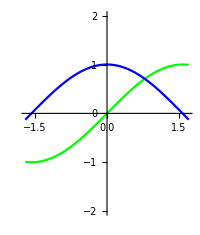

```mathematica
prob[Sin]
```

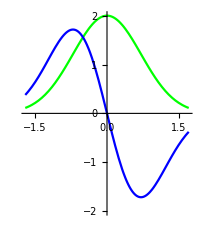

```mathematica
prob[2 Exp[-#^2]&]
```

## For MMConceptualComputational

```mathematica
Manipulate[
Show[
{
Plot[
{cu[x],tline[a,x],secline[a,a+h,x]
},{x,-1.7,1.7},
PlotRange->{{-1.7,1.7},{-2,2}},
PlotStyle->{Blue,Red,Brown},AspectRatio->40/34,ImageSize->250
],
Graphics[
{PointSize[.02],
Point[{a,cu[a]}],
Point[{a,cu[a]}],
Point[{a+h,cu[a+h]}]
}]
}
],{{a,-.85,"x"},-1.25,1.25},{{h,.5,"width"},.01,.7},
SaveDefinitions->True,Paneled->False]
```

```mathematica
dd=250/306//N
```

0.816993

```mathematica
175 dd
```

142.974

```mathematica
225 dd
```

183.824

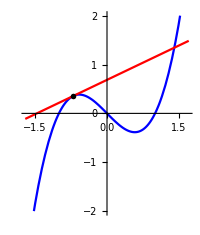

```mathematica
Module[{a=-.7,h=0},
Show[
{
Plot[
{cu[x],tline[a,x]
},{x,-1.7,1.7},
PlotRange->{{-1.7,1.7},{-2,2}},
PlotStyle->{Blue,Red,Brown},AspectRatio->40/34,ImageSize->200
],
Graphics[
{PointSize[.02],
Point[{a,cu[a]}]
}]
}
]
]
```

```mathematica
cu'[-0.7]
```

0.47

```mathematica
(cu[-0.7+0.01]-cu[-0.7])/0.01
```

0.4491

```mathematica
(cu[-0.7+0.001]-cu[-0.7])/0.001
```

0.467901

### Area Boxes

```mathematica
Style[s,FontSize->18,FontFamily->Arial]
```

s

```mathematica
mins[s_,p_]:=Inset[Text[Style[s,FontSize->14,FontFamily->Arial]],p]
```

```mathematica
mins[b,{.5,.1}]
```

Inset[b,{0.5,0.1}]

```mathematica
Pink//Lighter//Lighter
```

RGBColor[1, 0.7777777777777778, 0.7777777777777778]

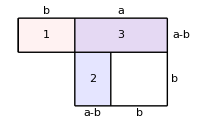

```mathematica
Module[{a=.9,b=.55,h=.07},
Show[
Graphics[
{Opacity[0.1],Pink,
Rectangle[
{0,0},{a+b,b-a}],
Blue,
Rectangle[
{b,0},{a+b,b-a}],
Blue,
Rectangle[
{b,b-a},{a,-a}],
Opacity[1],Black,
Line[{{0,0},{a+b,0}}],
Line[{{0,b-a},{a+b,b-a}}],
Line[{{b,-a},{a+b,-a}}],
Line[{{0,0},{0,b-a}}],
Line[{{0,0},{0,b-a}}],
Line[{{b,0},{b,-a}}],
Line[{{a,b-a},{a,-a}}],
Line[{{a+b,0},{a+b,-a}}],
mins["b",{.5b,h}],mins["a",{b+.5a,h}],mins["a-b",{a+b+2h,.5(b-a)}],mins["b",{a+b+h,.5b-a}],mins["a-b",{b+.5(a-b),-a-h}],mins["b",{a+.5b,-a-h}],
mins["1",{.5b,.5(b-a)}],
mins["2",{b+.5(a-b),b-a-.5b}],
mins["3",{b+.5a,.5(b-a)}]
},ImageSize->200,AspectRatio->a/(a+b)
]
]
]
```